# Reduction of intrapetrous artifact by rotation of sinogram

The recording of intensity of X-ray exposure by Computed Tomography detectors produces information that is displayed as a sinogram.  The sinogram information is then processed by the computer to give the diagnostically useful images in a way we understand the patient anatomy.   Artifacts may occur in the acquisition of the sinogram, or the reconstruction of tomographic sections in the transaxial, sagital, or coronal plane.  This is an example of processing the sinogram to reduce intrapetrous artifact on transaxial CT heads.  Intrapetrous artifact is commonly seen in CT heads overlying the brain stem, at the apex of the petrous bones.  The artifact reduces CT sensitivity for brain stem abnormalities.  The artifact is partially responsible (guess that part is only 10%... small part) for the preference for MRI for evaluation of brain stem lesions.  CT is still used more often in the emergency care setting.  Reduction of artifact would still help decision making.

This is a preliminary investigation, limited in scope of testing of only one of many reconstruction algorithms, and lacking real sinogram data.  This work just suggests that it might be worthwhile to test it on real sinogram data for those cases with significant artifact after reconstruction.  This is a test using a basic projection/filtered backprojection algorithm.  It is questionable whether it would be useful in Fourier transform modifications of filtered back projection, cardiac CT algorithms, or iterative algorithms

```mathematica
testCT=-Graphics-;
```

```mathematica
ImageDimensions[testCT]
```

{128,128}

```mathematica
radonCT=Radon[testCT]
```

-Graphics-

```mathematica
ImageAdjust[radonCT]
```

-Graphics-

The the typical sinogram is a Mobius strip.  The display in many available programs consists of the raysum data from 0 to 179 degrees (or Pi).  Because this algorithm is shifting the sinogram, data from the left side of the sinogram image must be flipped to match the data on the right side of the image.

```mathematica
{x,y}=ImageDimensions[radonCT];
```

The following will shift the sinogram data by 60 degrees.

```mathematica
{x,y}=ImageDimensions[radonCT];
imArray=Array[0,{1,2}];
imArray[[1,2]]=ImageTake[radonCT,{1,y},{1,x-60}];
imArray[[1,1]]=ImageReflect[ImageTake[radonCT,{1,y},{-60,-1}]];
nl=ImageAssemble[imArray];
ImageAdjust[r1=InverseRadon[nl]]
-Graphics-
```

-Graphics-

-Graphics-

The shift of the sinogram data results in a rotation of the reconstructed image.  Note that the artifact changes.

```mathematica
{x,y}=ImageDimensions[radonCT];
imArray[[1,2]]=ImageTake[radonCT,{1,y},{1,x-120}];
imArray[[1,1]]=ImageReflect[ImageTake[radonCT,{1,y},{-120,-1}]];
n2=ImageAssemble[imArray];
ImageAdjust[r2=InverseRadon[n2]]
```

-Graphics-

```mathematica
ImageAdjust[r3=InverseRadon[radonCT]]
```

-Graphics-

This demonstrates the intrapetrous artifact.   It is a band of decreased attenuation bounded by bands of increased attenuation.  Some of the artifact is related to the low resolution of the image, and the “half scan” nature of the sinogram.

```mathematica
a1=ImageAlign[r3,r1,TransformationClass->"Similarity"];
```

```mathematica
a2=ImageAlign[r3,r2,TransformationClass->"Similarity"];
```

```mathematica
datar3=Flatten[ImageData[r3]];
dataa2=Flatten[ImageData[a2]];
dataa1=Flatten[ImageData[a1]];
```

```mathematica
len=Length[datar3]
d4=ConstantArray[0.,len];
For[i=1,i≤ len,i++,d4[[i]]=Median[{datar3[[i]],dataa2[[i]],dataa1[[i]]}];];
```

73984

Artifact reduction is achieved by taking the median value of the three reconstructed (and then realigned) images.  Both the lowered attenuation, and the elevated attenuation artifact is reduced.

The following code is intended to show the level of the intrapetrous artifact.  The artifact extends across the entire image, but we are concerned with the artifact over the center of the image, the location of the brain stem.  The red line is about in the middle of the band of lowered attenuation crossing the brain stem, among other structures.

```mathematica
inverseCT=InverseRadon[radonCT];lines=ImageLines[inverseCT,.04,0.7];
HighlightImage[inverseCT,lines]//ImageAdjust
```

-Graphics-

The following displays the original image, the basic reconstructed image with the forward and reverse
Radon transform, and the image reconstructed using the median of the realigned rotated reconstructions.

```mathematica
ImageCollage[{ImageAdjust[testCT],ImageAdjust[inverseCT=InverseRadon[radonCT]],ImageAdjust[im=Image[Partition[d4,272]]]}]
```

-Graphics-

In order to restore some sharpness to the reconstructed image, I think it would be best to perform a reconstruction with a detail filter, then merge the images using the lower spatial, higher contrast images to demonstrate brain/soft tissue, and the higher spatial, lower contrast images to show bone and air.  Because the intrapetrous artifact does not affect the assessment of bone to the same degree as the brain stem, the bone detail image could be reconstructed without the sinogram shifting process.  When dealing with the artifact from metal implants, the same sinogram shifting process would likely reduce the metal artifact.  The following code simulates that process (however, I am fusing the original image with the reconstructed image).  If the algorithm is used with real sinogram data, I would reconstruct a transaxial image  with both detail “bone” or high frequency filter, and a “soft tissue” or low frequency, low noise filter.  If I was working with reconstructed images normalized to the Hounsfield scale, I would use pixel thresholds based on Hounsfield measures of bone density, and air density.

```mathematica
fltestCT=Flatten[ImageData[testCT]];
```

```mathematica
flim=Flatten[ImageData[ImageResize[im,128]]];
```

```mathematica
n=Length[fltestCT];
```

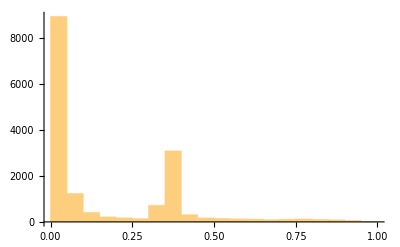

```mathematica
Histogram[fltestCT]
```

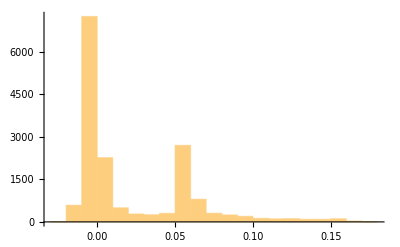

```mathematica
Histogram[flim]
```

After the reconstruction process, normalization of data is needed to reflect the expected values (Hounsfield units).  For generalized image processing, Mathematica uses data scaled between 0 and 1. In order to partially normalize the data between the original image, and reconstructed image, I just looked at the histograms of the 2 images.  The first peak is the background of the CT image.  The second peak is the soft tissues, trailing off to the bone densities spreading out higher than soft tissue densities.  I just approximated the difference between the second peaks in both histograms.  Not rigorous, but quick.  That is the reason for multiplying the pixel densities of the reconstructed soft tissue image with a factor of 7.5.

This demonstrates how different components of images reconstructed with different filters could be combined to show high detail in some areas, and high contrast resolution within the brain.

```mathematica
altim= ConstantArray[0,n];
```

```mathematica
For[i=1,i≤n,i++,If[(fltestCT[[i]]< .2 )|| (fltestCT[[i]] > .35), altim[[i]]=fltestCT[[i]], altim[[i]]=7.5*flim[[i]]]];
```

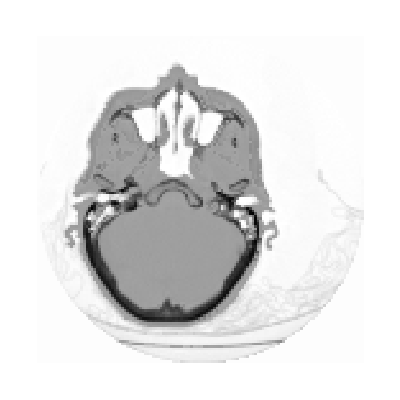

```mathematica
ArrayPlot[newarray=Partition[altim,128]]
```

```mathematica
ImageAdjust[Image[newarray]]
```

-Graphics-

In summary, this program demonstrates a technique that projects reconstruction artifact onto different pixels of a reconstructed CT head image.  By taking the median of the pixels of 3 or more reconstructed, rotated images, the pixels with the greatest positive or negative values (those pixels affected by artifact) are eliminated leaving the pixels with the least artifact for the final image.  This technique may or may not prove useful if combined with the more sophisticated tomographic reconstruction algorithms currently used on CT machines for clinical use.

As a mathematical side note, the sinogram (as typically constructed) has some of the properties of a Mobius Strip.

Many thanks to the programmers at Mathematica that provided the bulk of this code in the examples provided in the documentation of functions.  I am not a professional programmer, and it shows.  Often I revert to procedural programming from my experience with good ole “C”.  Mathematica does have many nice functional programming procedures which I have not taken advantage.